```mathematica
Guy F. Mongelli
Prof. J. Admin Mann
ECHE 475
9/19/2012
```

```mathematica
Problem 1:
```

```mathematica
let the vector f be defined as
```

```mathematica
let x,y, and z be defined as follows:
```

```mathematica
x=r*Sin[θ]*Cos[ϕ]
y=r*Sin[θ]Sin[ϕ]
z=r*Cos[θ]
```

r Cos[ϕ] Sin[θ]

r Sin[θ] Sin[ϕ]

r Cos[θ]

```mathematica
f=MatrixForm[({{x}, {y}, {z}})]
```

(r Cos[ϕ] Sin[θ]
r Sin[θ] Sin[ϕ]
r Cos[θ])

```mathematica
df=MatrixForm[({{D[x,r], D[x,θ], D[x,ϕ]}, {D[y,r], D[y,θ], D[y,ϕ]}, {D[z,r], D[z,θ], D[z,ϕ]}})]
```

(Cos[ϕ] Sin[θ] | r Cos[θ] Cos[ϕ] | -r Sin[θ] Sin[ϕ]
Sin[θ] Sin[ϕ] | r Cos[θ] Sin[ϕ] | r Cos[ϕ] Sin[θ]
Cos[θ] | -r Sin[θ] | 0)

```mathematica
df=MatrixForm[FullSimplify[({{D[x,r], D[x,θ], D[x,ϕ]}, {D[y,r], D[y,θ], D[y,ϕ]}, {D[z,r], D[z,θ], D[z,ϕ]}})]]
```

(Cos[ϕ] Sin[θ] | r Cos[θ] Cos[ϕ] | -r Sin[θ] Sin[ϕ]
Sin[θ] Sin[ϕ] | r Cos[θ] Sin[ϕ] | r Cos[ϕ] Sin[θ]
Cos[θ] | -r Sin[θ] | 0)

```mathematica
We can force Mathematica to give us the jacobian matrix and it's determinanat of any corrdinate system that we should like.  Even relative to other coordinate system transofrmations.
```

```mathematica
Needs["VectorAnalysis`"];
```

```mathematica
JacobianMatrix[{r, θ, ϕ}, Spherical]//MatrixForm
```

(Cos[ϕ] Sin[θ] | r Cos[θ] Cos[ϕ] | -r Sin[θ] Sin[ϕ]
Sin[θ] Sin[ϕ] | r Cos[θ] Sin[ϕ] | r Cos[ϕ] Sin[θ]
Cos[θ] | -r Sin[θ] | 0)

```mathematica
Det[%]//Simplify
```

r^2 Sin[θ]

```mathematica
JacobianDeterminant[{r, θ,ϕ}, Spherical]
```

r^2 Sin[θ]

```mathematica
For the other coordinate system transformations of interest:
```

```mathematica
JacobianMatrix[{x, y, z},Cartesian]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
JacobianDeterminant[{x, y, z},Cartesian]
```

1

```mathematica
JacobianMatrix[{x, y, z},Cylindrical]//MatrixForm
```

(Cos[r Sin[θ] Sin[ϕ]] | -r Cos[ϕ] Sin[θ] Sin[r Sin[θ] Sin[ϕ]] | 0
Sin[r Sin[θ] Sin[ϕ]] | r Cos[ϕ] Cos[r Sin[θ] Sin[ϕ]] Sin[θ] | 0
0 | 0 | 1)

```mathematica
JacobianDeterminant[{x, y, z},Cylindrical]
```

r Cos[ϕ] Sin[θ]

```mathematica
Problem 2:
```

2 Problem

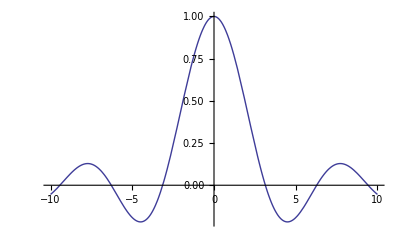

```mathematica
Plot[Sin[x]/x,{x,-10,10}]
```

```mathematica
The first value returned is the global maximum of the function.  The second value is the corresponding x-value.  Note that the x-value is close enought to zero to be defined as just that.
```

```mathematica
FindMaximum[Sin[a]/a,a]
```

{1.,{a→5.13483×10^-10}}

```mathematica
The first value returned is the global minimum of the function.  The second value is the correspondinx x-value which is close enough to
```

```mathematica
FindMinimum[Sin[a]/a,a]
```

{-0.217234,{a→4.49341}}

```mathematica
s[a_]=FullSimplify[D[Sin[a]/a,a]]
```

(a Cos[a]-Sin[a])/a^2

```mathematica
The global minimum and maximum specify the codomain.  This can be represented as [-.217,1].  The domain is all reals except for 0.
```

```mathematica
Problem 3:
```

```mathematica
ComplexExpand[Log[a+ⅈ*b]]
```

ⅈ Arg[a+ⅈ b]+1/2 Log[a^2+b^2]

```mathematica
The following expansion makes use of Euler's formula:
```

```mathematica
ComplexExpand[Exp[a+ⅈ*b]]
```

ⅇ^a Cos[b]+ⅈ ⅇ^a Sin[b]

```mathematica
If we consider the complex plane, we may substitute x for a and y for i*b, realizing that these coordinates have the same orthogonality condition.  Then these functions can be understood in terms of a 3D plot.
```

```mathematica
t[x_,y_]=Log[x+y]
```

Log[a+ⅈ b]

```mathematica
s[x_,y_]=Exp[x+y]
```

ⅇ^(a+ⅈ b)

```mathematica
The two methods for understanding the complex plane are (i) to fix either a or b and plot the function as it relates to the non-fixed variable or (ii) to plot a contour map.  Both or these are done here.  The domain of one system becomes the codomain of the other and visa-versa since these are inverse functions.
```

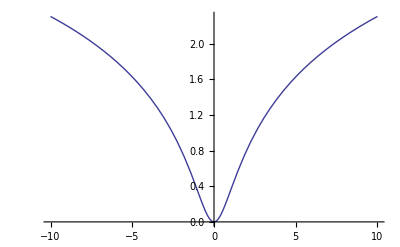

```mathematica
Plot[Re[t[x,1]],{x,-10,10}]
```

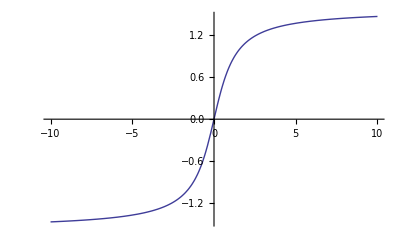

```mathematica
Plot[Im[t[1,b]],{b,-10,10}]
```

```mathematica
Plot3D[Log[a+b],{a,-10,10},{b,-10,10},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[Exp[a+b],{a,-10,10},{b,-10,10},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
We know that these functions are inverses because compounding them returns the identity element for this function: a+b.
```

```mathematica
Plot3D[Exp[Log[a+b]],{a,-10,10},{b,-10,10},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Problem 4:
```

```mathematica
Clear[x,y,z]
```

```mathematica
Part A:
```

```mathematica
Part B:
```

```mathematica
Instead of x and Subscript[x, n],m and Subscript[m, n] will be used such that variables will not be duplicated in this notebook.  Subscript[m, n] will be written as a function to be later defined.(Note: writting Subscript[m, n] in the cell produces an empty response in the Fourier transform function, but writing it m[n] works fine).
```

```mathematica
ρ[x_]=∑_(n=1)^N DiracDelta[x-x[n]]
```

∑_(n=1)^N DiracDelta[m-m[n]]

```mathematica
To show this is equivalent to the definition
```

```mathematica
FullSimplify[∫_(-∞)^∞ Exp[-2Pi*ⅈ*x]*(∑_(n=1)^N DiracDelta[x-x[n]])ⅆx]
```

∫_(-∞)^∞ ⅇ^(-2 ⅈ π x) ∑_(n=1)^N DiracDelta[x-x[n]]ⅆx

```mathematica
Ρ[q_]=FourierTransform[ρ[m],m,q]
```

∑_(n=1)^N ⅇ^(ⅈ q m[n])/(√(2 π))

```mathematica
m[n_]=
```